## These plots are generated in BC_CumulativeBeta.nb

## BrownAn00

```mathematica
Print[DateSequence[DateList[],"yes"]];
MatrixNote[Tmat]
PrintVoigt[Tmat]
Print[" UforNM1 = ", MatrixForm[UforNM1]];
```

12-31-2023 6:5

T is BrownAn00

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {204.263,179.169,75.8705,60.7101,50.1339,33.4538}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -9.2 | 7.5 | -9.4
4.9 | -4.4 | -9.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

12-31-2023 6:5

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.454 = 26.037^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

UforNM1 = (0.921451 | -0.368714 | -0.12239
-0.365504 | -0.929543 | 0.0485472
-0.131666 | 0. | -0.991294)

#### List all angles for all node sequences and all node modes

```mathematica
nodeSequences={ΣnTETXISO,ΣnTETCUBE,ΣnTRIGXISO,ΣnTRIGCUBE};
nodeModes={nm1,nm2,nm3};
results=Flatten[Table[{DisplayAngles[nodeSeq,nodeMode],"\n\n"},
{nodeSeq,nodeSequences},{nodeMode,nodeModes}],1];
StringJoin[results]//Print
```

node sequence is ΣnTETXISO, node mode is nm1
TRIV-MONO     6.76    TRIV..MONO     6.76
MONO-ORTH    12.91    TRIV..ORTH    19.67
 ORTH-TET    11.69     TRIV..TET    31.36
 TET-XISO     1.11    TRIV..XISO    32.47
 XISO-ISO    18.54     TRIV..ISO    51.00

node sequence is ΣnTETXISO, node mode is nm2
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-ORTH     5.22    TRIV..ORTH     8.99
 ORTH-TET     4.82     TRIV..TET    13.81
 TET-XISO    17.92    TRIV..XISO    31.74
 XISO-ISO    18.54     TRIV..ISO    50.27

node sequence is ΣnTETXISO, node mode is nm3
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-ORTH     5.21    TRIV..ORTH     8.98
 ORTH-TET     4.69     TRIV..TET    13.67
 TET-XISO    17.69    TRIV..XISO    31.36
 XISO-ISO    17.77     TRIV..ISO    49.14

node sequence is ΣnTETCUBE, node mode is nm1
TRIV-MONO     6.76    TRIV..MONO     6.76
MONO-ORTH    12.91    TRIV..ORTH    19.67
 ORTH-TET    11.69     TRIV..TET    31.36
 TET-CUBE    13.70    TRIV..CUBE    45.06
 CUBE-ISO    12.66     TRIV..ISO    57.72

node sequence is ΣnTETCUBE, node mode is nm2
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-ORTH     5.22    TRIV..ORTH     8.99
 ORTH-TET     4.82     TRIV..TET    13.81
 TET-CUBE    19.76    TRIV..CUBE    33.57
 CUBE-ISO    15.59     TRIV..ISO    49.16

node sequence is ΣnTETCUBE, node mode is nm3
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-ORTH     5.21    TRIV..ORTH     8.98
 ORTH-TET     4.69     TRIV..TET    13.67
 TET-CUBE    19.72    TRIV..CUBE    33.40
 CUBE-ISO    15.47     TRIV..ISO    48.87

node sequence is ΣnTRIGXISO, node mode is nm1
TRIV-MONO     6.76    TRIV..MONO     6.76
MONO-TRIG    17.55    TRIV..TRIG    24.30
TRIG-XISO     2.41    TRIV..XISO    26.72
 XISO-ISO    18.54     TRIV..ISO    45.25

node sequence is ΣnTRIGXISO, node mode is nm2
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-TRIG    16.47    TRIV..TRIG    20.24
TRIG-XISO    20.68    TRIV..XISO    40.92
 XISO-ISO    18.54     TRIV..ISO    59.46

node sequence is ΣnTRIGXISO, node mode is nm3
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-TRIG    16.13    TRIV..TRIG    19.90
TRIG-XISO    12.95    TRIV..XISO    32.85
 XISO-ISO    15.88     TRIV..ISO    48.73

node sequence is ΣnTRIGCUBE, node mode is nm1
TRIV-MONO     6.76    TRIV..MONO     6.76
MONO-TRIG    17.55    TRIV..TRIG    24.30
TRIG-CUBE    13.19    TRIV..CUBE    37.50
 CUBE-ISO    12.66     TRIV..ISO    50.16

node sequence is ΣnTRIGCUBE, node mode is nm2
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-TRIG    16.47    TRIV..TRIG    20.24
TRIG-CUBE    22.40    TRIV..CUBE    42.65
 CUBE-ISO    15.59     TRIV..ISO    58.24

node sequence is ΣnTRIGCUBE, node mode is nm3
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-TRIG    16.13    TRIV..TRIG    19.90
TRIG-CUBE    15.57    TRIV..CUBE    35.47
 CUBE-ISO    13.33     TRIV..ISO    48.80

#### Sequentially add nm1, nm2, nm3 to each plot

```mathematica
Print["Node sequence is ",range[Σn]];
GraphicsForCumulative[Tmat,Σn,"WantDirect","noWantNM1","noWantNM2","noWantNM3"]
GraphicsForCumulative[Tmat,Σn,"WantDirect","WantNM1","noWantNM2","noWantNM3"]
GraphicsForCumulative[Tmat,Σn,"WantDirect","WantNM1","WantNM2","noWantNM3"]
GraphicsForCumulative[Tmat,Σn,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### direct, nm1, nm2, nm3 for four different node sequences

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## BrownAn00Pert

```mathematica
Print[DateSequence[DateList[],"yes"]];
MatrixNote[Tmat]
PrintVoigt[Tmat]
Print[" UforNM1 = ", MatrixForm[UforNM1]];
```

12-31-2023 5:36

T is BrownAn00Pert

The [T]_𝔹𝔹 matrix is (28.308 | -7.968 | -23.904 | -15.438 | 18.1138 | -11.7918
-7.968 | 34.616 | 1.992 | -9.13 | -24.0559 | -3.524
-23.904 | 1.992 | 56.86 | -9.13 | 11.0216 | -22.6349
-15.438 | -9.13 | -9.13 | 101.514 | 79.9307 | 61.3989
18.1138 | -24.0559 | 11.0216 | 79.9307 | 193.035 | -30.6752
-11.7918 | -3.524 | -22.6349 | 61.3989 | -30.6752 | 189.267)

The eigenvalues are: {243.339,223.134,71.2524,38.8629,26.5166,0.494292}

The Voigt matrix is (35.278 | 30.044 | 27.056 | 8.134 | -3.818 | -1.494
30.044 | 227.838 | -15.108 | -7.304 | -12.948 | -10.624
27.056 | -15.108 | 220.7 | -15.272 | 12.45 | -15.604
8.134 | -7.304 | -15.272 | 14.154 | -3.984 | -11.952
-3.818 | -12.948 | 12.45 | -3.984 | 17.308 | 0.996
-1.494 | -10.624 | -15.604 | -11.952 | 0.996 | 28.43)

12-31-2023 5:36

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 214.796   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.681 = 39.04^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

UforNM1 = (0.921451 | -0.368714 | -0.12239
-0.365504 | -0.929543 | 0.0485472
-0.131666 | 0. | -0.991294)

#### List all angles for all node sequences and all node modes

```mathematica
nodeSequences={ΣnTETXISO,ΣnTETCUBE,ΣnTRIGXISO,ΣnTRIGCUBE};
nodeModes={nm1,nm2,nm3};
results=Flatten[Table[{DisplayAngles[nodeSeq,nodeMode],"\n\n"},
{nodeSeq,nodeSequences},{nodeMode,nodeModes}],1];
StringJoin[results]//Print
```

node sequence is ΣnTETXISO, node mode is nm1
TRIV-MONO     9.72    TRIV..MONO     9.72
MONO-ORTH    18.85    TRIV..ORTH    28.57
 ORTH-TET    17.56     TRIV..TET    46.13
 TET-XISO     1.69    TRIV..XISO    47.82
 XISO-ISO    29.10     TRIV..ISO    76.92

node sequence is ΣnTETXISO, node mode is nm2
TRIV-MONO     5.42    TRIV..MONO     5.42
MONO-ORTH     7.52    TRIV..ORTH    12.94
 ORTH-TET     6.97     TRIV..TET    19.91
 TET-XISO    26.49    TRIV..XISO    46.40
 XISO-ISO    29.10     TRIV..ISO    75.50

node sequence is ΣnTETXISO, node mode is nm3
TRIV-MONO     5.42    TRIV..MONO     5.42
MONO-ORTH     7.51    TRIV..ORTH    12.92
 ORTH-TET     6.79     TRIV..TET    19.71
 TET-XISO    26.14    TRIV..XISO    45.85
 XISO-ISO    28.02     TRIV..ISO    73.87

node sequence is ΣnTETCUBE, node mode is nm1
TRIV-MONO     9.72    TRIV..MONO     9.72
MONO-ORTH    18.85    TRIV..ORTH    28.57
 ORTH-TET    17.56     TRIV..TET    46.13
 TET-CUBE    21.23    TRIV..CUBE    67.36
 CUBE-ISO    20.45     TRIV..ISO    87.81

node sequence is ΣnTETCUBE, node mode is nm2
TRIV-MONO     5.42    TRIV..MONO     5.42
MONO-ORTH     7.52    TRIV..ORTH    12.94
 ORTH-TET     6.97     TRIV..TET    19.91
 TET-CUBE    29.35    TRIV..CUBE    49.26
 CUBE-ISO    24.85     TRIV..ISO    74.11

node sequence is ΣnTETCUBE, node mode is nm3
TRIV-MONO     5.42    TRIV..MONO     5.42
MONO-ORTH     7.51    TRIV..ORTH    12.92
 ORTH-TET     6.79     TRIV..TET    19.71
 TET-CUBE    29.30    TRIV..CUBE    49.01
 CUBE-ISO    24.67     TRIV..ISO    73.68

node sequence is ΣnTRIGXISO, node mode is nm1
TRIV-MONO     9.72    TRIV..MONO     9.72
MONO-TRIG    25.84    TRIV..TRIG    35.56
TRIG-XISO     3.68    TRIV..XISO    39.25
 XISO-ISO    29.10     TRIV..ISO    68.35

node sequence is ΣnTRIGXISO, node mode is nm2
TRIV-MONO     5.42    TRIV..MONO     5.42
MONO-TRIG    24.06    TRIV..TRIG    29.48
TRIG-XISO    31.57    TRIV..XISO    61.05
 XISO-ISO    29.10     TRIV..ISO    90.15

node sequence is ΣnTRIGXISO, node mode is nm3
TRIV-MONO     5.42    TRIV..MONO     5.42
MONO-TRIG    23.55    TRIV..TRIG    28.97
TRIG-XISO    19.74    TRIV..XISO    48.71
 XISO-ISO    25.28     TRIV..ISO    73.99

node sequence is ΣnTRIGCUBE, node mode is nm1
TRIV-MONO     9.72    TRIV..MONO     9.72
MONO-TRIG    25.84    TRIV..TRIG    35.56
TRIG-CUBE    20.40    TRIV..CUBE    55.97
 CUBE-ISO    20.45     TRIV..ISO    76.42

node sequence is ΣnTRIGCUBE, node mode is nm2
TRIV-MONO     5.42    TRIV..MONO     5.42
MONO-TRIG    24.06    TRIV..TRIG    29.48
TRIG-CUBE    34.53    TRIV..CUBE    64.01
 CUBE-ISO    24.85     TRIV..ISO    88.87

node sequence is ΣnTRIGCUBE, node mode is nm3
TRIV-MONO     5.42    TRIV..MONO     5.42
MONO-TRIG    23.55    TRIV..TRIG    28.97
TRIG-CUBE    23.86    TRIV..CUBE    52.82
 CUBE-ISO    21.48     TRIV..ISO    74.30

#### Sequentially add nm1, nm2, nm3 to each plot

```mathematica
Print["Node sequence is ",range[Σn]];
GraphicsForCumulative[Tmat,Σn,"WantDirect","noWantNM1","noWantNM2","noWantNM3"]
GraphicsForCumulative[Tmat,Σn,"WantDirect","WantNM1","noWantNM2","noWantNM3"]
GraphicsForCumulative[Tmat,Σn,"WantDirect","WantNM1","WantNM2","noWantNM3"]
GraphicsForCumulative[Tmat,Σn,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### direct, nm1, nm2, nm3 for four different node sequences

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## BrownAn25

#### Sequentially add nm1, nm2, nm3 to each plot

12-7-2023 5:32

T is BrownAn25

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.983909 | -0.154509 | -0.0897222
-0.153871 | -0.987991 | 0.0140314
-0.0908127 | 0. | -0.995868)

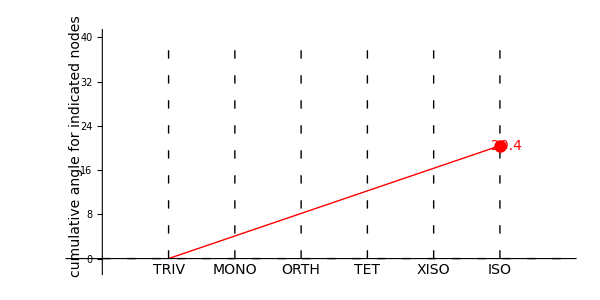

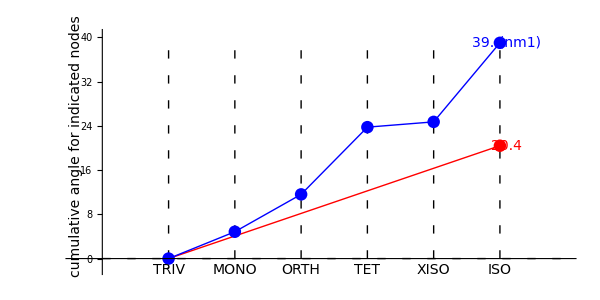

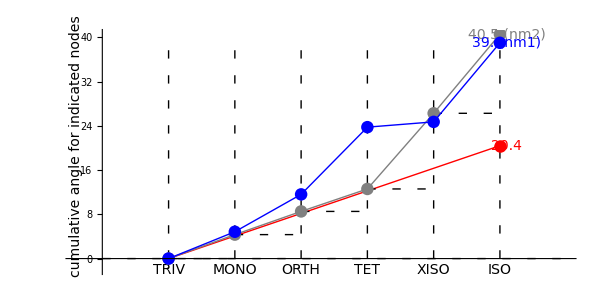

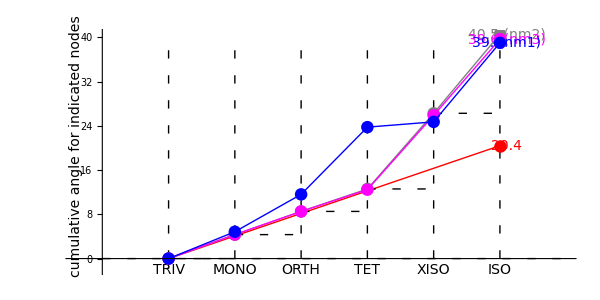

#### direct, nm1, nm2, nm3 for four different node sequences

-Graphics-

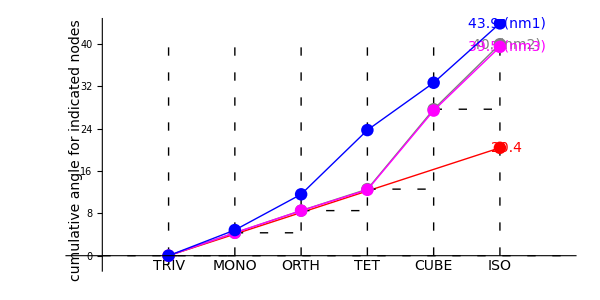

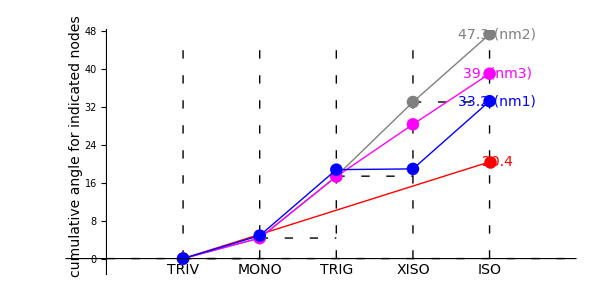

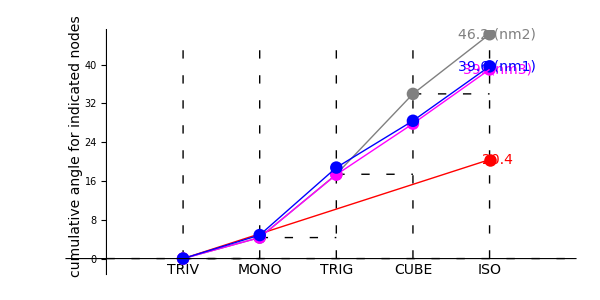

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

## BrownAn37

#### Sequentially add nm1, nm2, nm3 to each plot

12-7-2023 5:54

T is BrownAn37

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.0025682 | -0.99849 | -0.0548752
-0.0466789 | -0.0549353 | 0.997398
-0.998907 | 0. | -0.0467495)

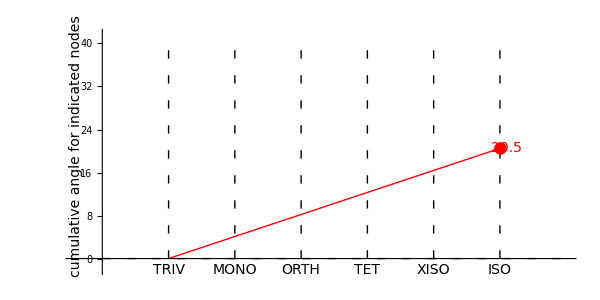

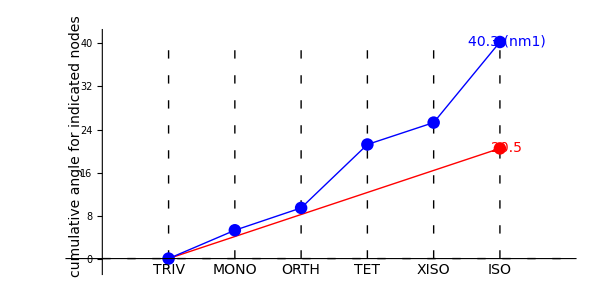

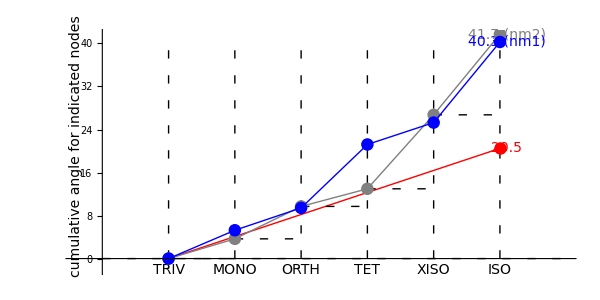

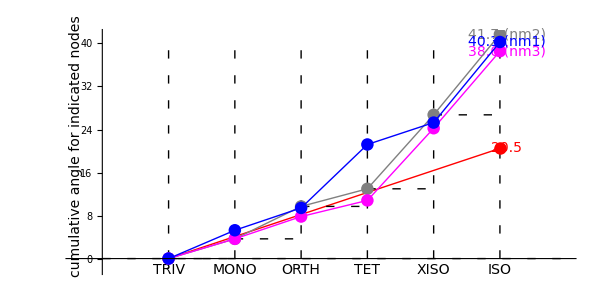

#### direct, nm1, nm2, nm3 for four different node sequences

-Graphics-

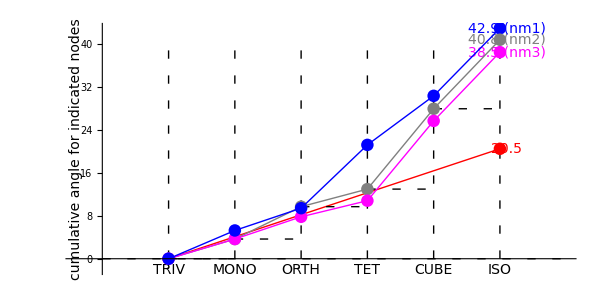

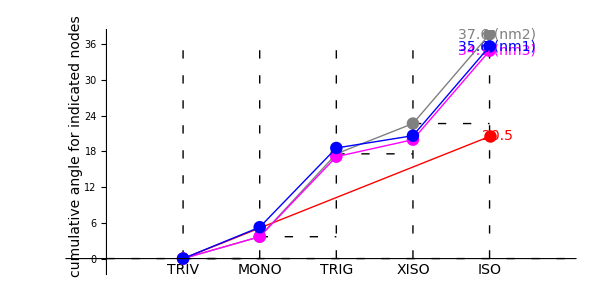

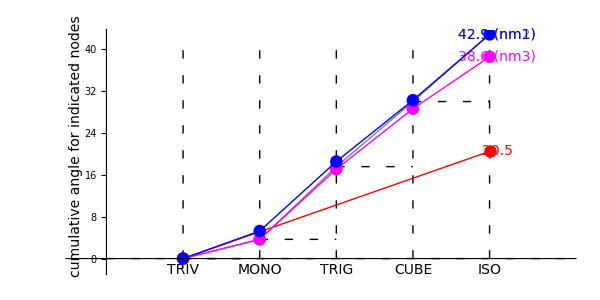

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

## BrownAn48

#### Sequentially add nm1, nm2, nm3 to each plot

12-7-2023 6:21

T is BrownAn48

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.000955066 | -0.994924 | -0.100625
-0.00944278 | -0.100629 | 0.994879
-0.999955 | 0. | -0.00949095)

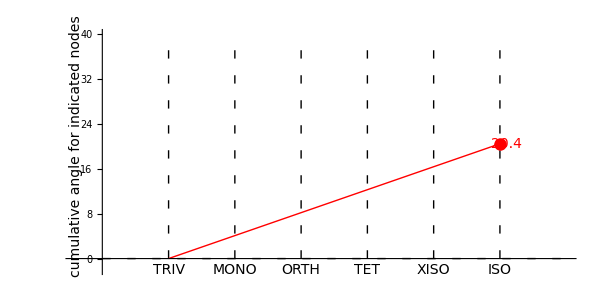

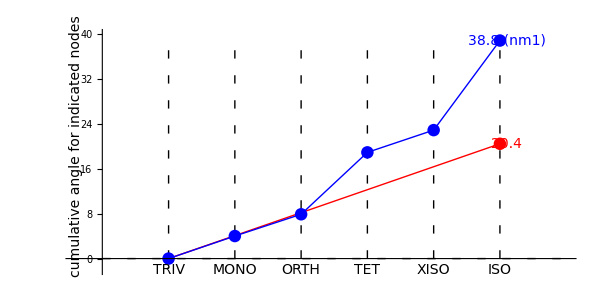

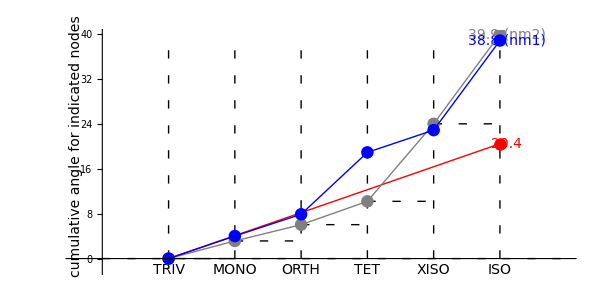

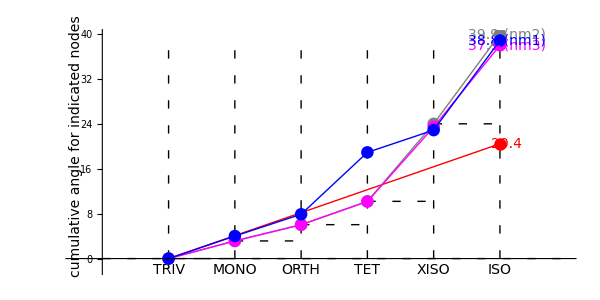

#### direct, nm1, nm2, nm3 for four different node sequences

-Graphics-

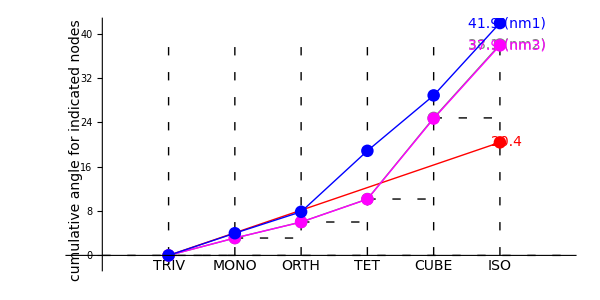

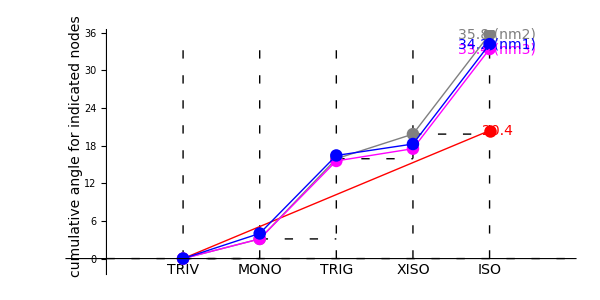

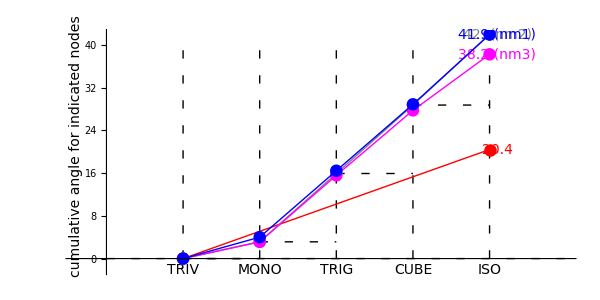

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

## BrownAn60

#### Sequentially add nm1, nm2, nm3 to each plot

12-7-2023 6:39

T is BrownAn60

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.00221262 | -0.997378 | -0.0723372
-0.0304931 | -0.0723711 | 0.996912
-0.999533 | 0. | -0.0305733)

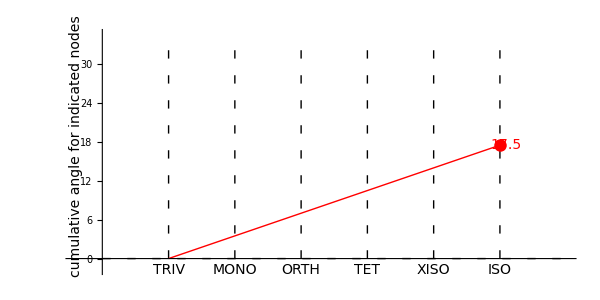

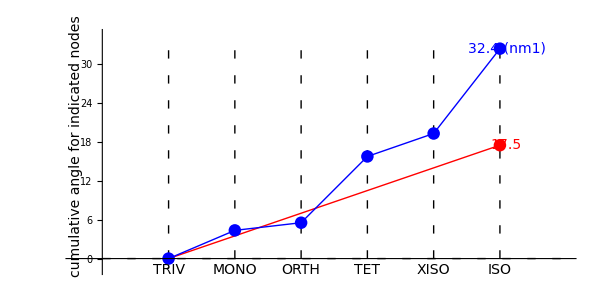

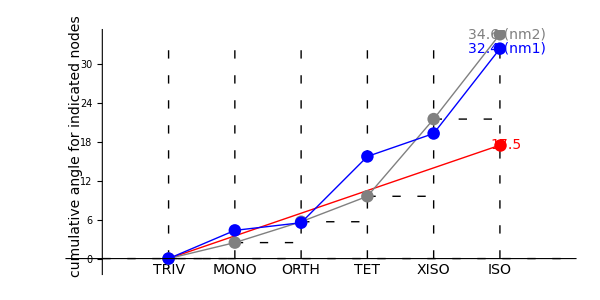

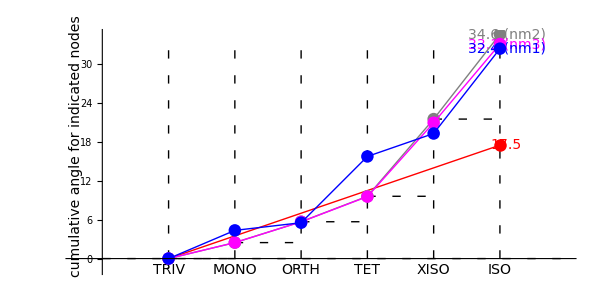

#### direct, nm1, nm2, nm3 for four different node sequences

-Graphics-

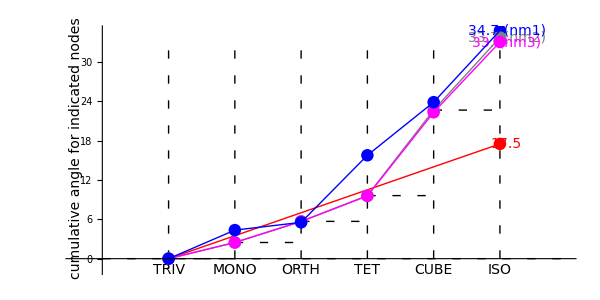

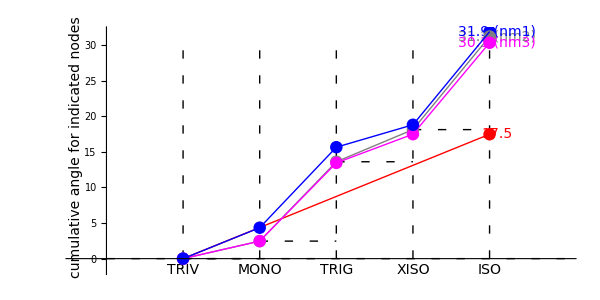

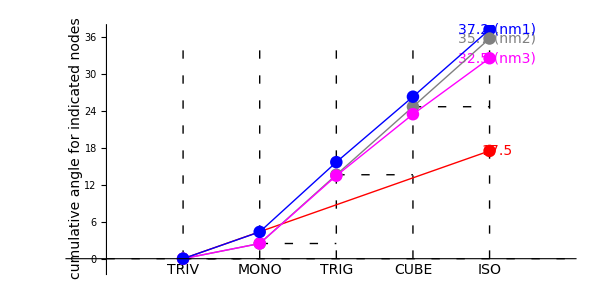

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

## BrownAn78

#### Sequentially add nm1, nm2, nm3 to each plot

12-7-2023 6:56

T is BrownAn78

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.000961598 | -0.993893 | -0.110347
-0.00866079 | -0.110351 | 0.993855
-0.999962 | 0. | -0.00871401)

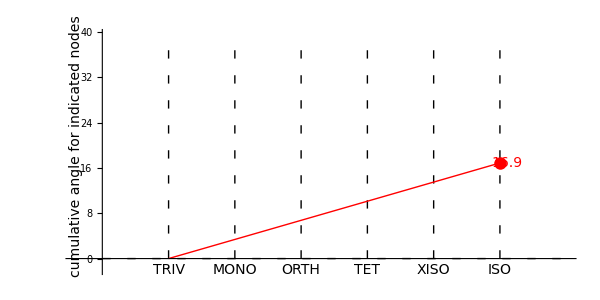

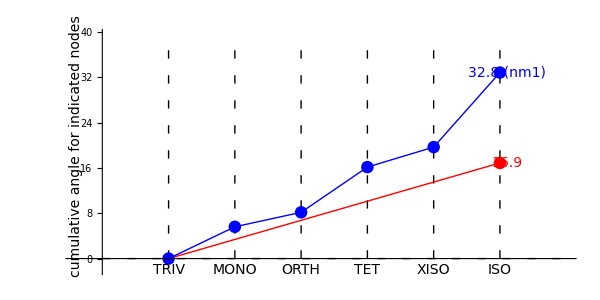

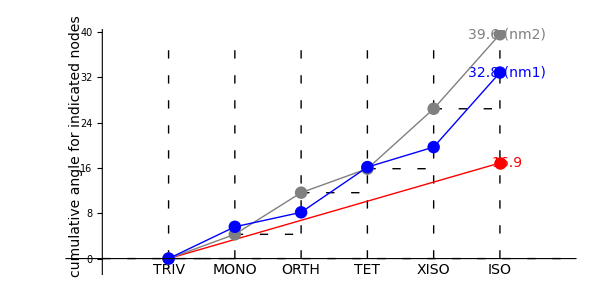

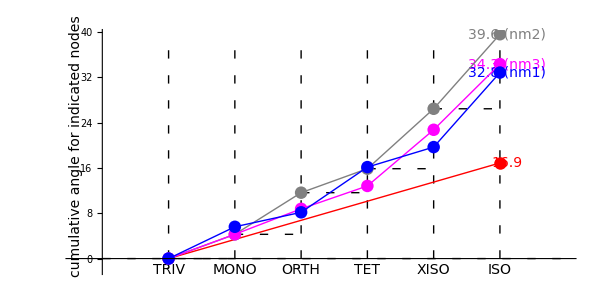

#### direct, nm1, nm2, nm3 for four different node sequences

-Graphics-

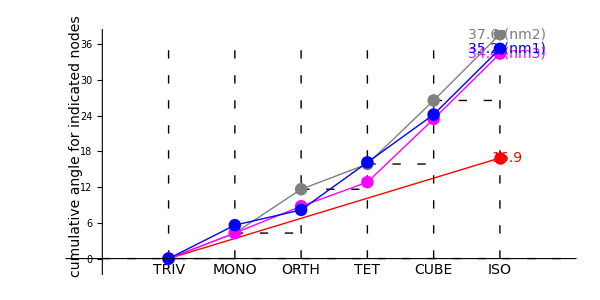

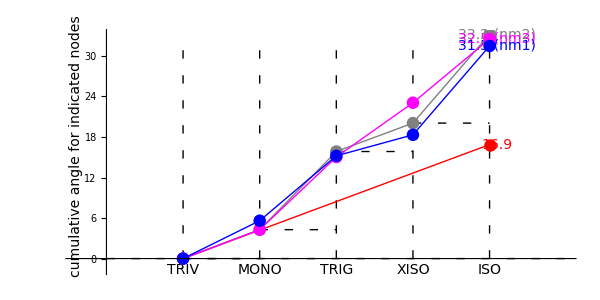

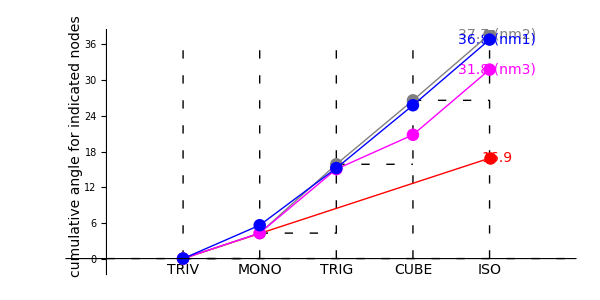

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

## BrownAn96

#### Sequentially add nm1, nm2, nm3 to each plot

12-20-2023 22:36

T is BrownAn96

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (-0.00137287 | -0.997863 | -0.0653337
0.0209636 | -0.0653481 | 0.997642
-0.999779 | 0. | 0.0210085)

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### direct, nm1, nm2, nm3 for four different node sequences

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## Igel

#### Sequentially add nm1, nm2, nm3 to each plot

12-21-2023 9:49

T is Igel

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.0498003 | -0.997825 | 0.0431815
0.753887 | 0.0659144 | 0.65369
-0.655115 | 0. | 0.75553)

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### direct, nm1, nm2, nm3 for four different node sequences

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## SSA2023

#### Sequentially add nm1, nm2, nm3 to each plot

12-21-2023 12:35

T is SSA2023

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.116812 | -0.955654 | 0.270334
0.379065 | 0.294492 | 0.87726
-0.917968 | 0. | 0.396655)

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### direct, nm1, nm2, nm3 for four different node sequences

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## Mar17

#### Sequentially add nm1, nm2, nm3 to each plot

12-21-2023 21:26

T is Mar17

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (0.261187 | -0.95316 | 0.152536
0.823076 | 0.302466 | 0.480686
-0.504308 | 0. | 0.863524)

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### direct, nm1, nm2, nm3 for four different node sequences

```mathematica
GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"]
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-